```mathematica
Clear["Global`*"]
```

```mathematica
Clear[α,hbar,m,k0,t,w,x,N0]
```

```mathematica
$Assumptions={α>0,hbar>0,m>0,{k0,t,w,x,N0}∈ Reals}
```

{α>0,hbar>0,m>0,(k0|t|w|x|N0)∈ℝ}

```mathematica
Ft[k_]:=Exp[-α(k-k0)^2]
```

```mathematica
N0=Integrate[Ft[k]*Conjugate[Ft[k]],{k,-Infinity,Infinity}]
```

(√(π/2))/(√α)

```mathematica
Ft1[k_]:=Sqrt[1/N0] Exp[-α(k-k0)^2]
```

```mathematica
ω[k_]:=hbar k^2/(2 m)
```

```mathematica
ψ[x_,t_]:=1/Sqrt[2 π] Integrate[Ft1[k] Exp[I (k x-ω[k] t)],{k,-Infinity,Infinity},Assumptions->$Assumptions]
```

```mathematica
ψSimplificado[x_,t_]:=FullSimplify[ψ[x,t],Assumptions->$Assumptions]
```

```mathematica
ψSimplificado[x,t]
```

(ⅇ^((-2 hbar k0^2 t α+m x (ⅈ x+4 k0 α))/(2 hbar t-4 ⅈ m α)) (2/π)^(1/4) α^(1/4))/(√((ⅈ hbar t)/m+2 α))

```mathematica
DensidadProbabilidad[x_,t_]:=Abs[ψ[x,t]]^2
```

```mathematica
DensidadProbabilidadSimplificada[x_,t_]:=FullSimplify[DensidadProbabilidad[x,t],Assumptions->$Assumptions]
```

```mathematica
DensidadProbabilidadSimplificada[x,t]
```

(ⅇ^(2 Re[(-2 hbar k0^2 t α+m x (ⅈ x+4 k0 α))/(2 hbar t-4 ⅈ m α)]) √(2/π) √α)/Abs[(ⅈ hbar t)/m+2 α]

```mathematica
Pk[k_]:=Ft1[k]*Conjugate[Ft1[k]]
```

```mathematica
medk=Integrate[k*Pk[k],{k,-Infinity,Infinity}]
```

k0

```mathematica
vark=Integrate[k^2*Pk[k],{k,-Infinity,Infinity}]
```

k0^2+1/(4 α)

```mathematica
Δk=Sqrt[vark-medk^2]
```

(√(1/α))/2

```mathematica
P[x_,t_]:=ψ[x,t]*Conjugate[ψ[x,t]]
```

```mathematica
medx=Integrate[x*P[x,t],{x,-Infinity,Infinity}]
```

(hbar k0 t √(-ⅈ hbar t+2 m α) Conjugate[1/(√((ⅈ hbar t)/m+2 α))])/m^(3/2)

```mathematica
varx=Integrate[x^2*P[x,t],{x,-Infinity,Infinity}]
```

(√(-ⅈ hbar t+2 m α) (4 m^2 α^2+hbar^2 t^2 (1+4 k0^2 α)) Conjugate[1/(√((ⅈ hbar t)/m+2 α))])/(4 m^(5/2) α)

```mathematica
Δx=Sqrt[varx-medx^2]
```

√((√(-ⅈ hbar t+2 m α) (4 m^2 α^2+hbar^2 t^2 (1+4 k0^2 α)) Conjugate[1/(√((ⅈ hbar t)/m+2 α))])/(4 m^(5/2) α)-(hbar^2 k0^2 t^2 (-ⅈ hbar t+2 m α) Conjugate[1/(√((ⅈ hbar t)/m+2 α))]^2)/m^3)

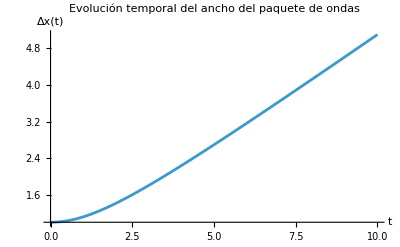

```mathematica
Plot[Δx,{t,0,10},AxesLabel->{"t","Δx(t)"},PlotLabel->"Evolución temporal del ancho del paquete de ondas",PlotRange->All]
```

```mathematica
Ψ0[k_,0]:=FourierTransform[ψ[x,0],x,k]
```

```mathematica
P0[x_,0]:=Abs[ψ[x,0]]^2
```

```mathematica
Pk0[k_,0]:=Abs[Ψ0[k,0]]^2
```

```mathematica
medx0=Integrate[x*P0[x,0],{x,-Infinity,Infinity}]
```

0

```mathematica
varx0=Integrate[x^2*P0[x,0],{x,-Infinity,Infinity}]
```

α

```mathematica
medk0=Integrate[k*Pk0[k,0],{k,-Infinity,Infinity}]
```

-k0

```mathematica
vark0=Integrate[k^2*Pk0[k,0],{k,-Infinity,Infinity}]
```

k0^2+1/(4 α)

```mathematica
Δx0=Sqrt[varx0-medx0^2]
```

1

```mathematica
Δk0=Sqrt[vark0-medk0^2]
```

1/2

```mathematica
Print["Δx = ",Δx0];
Print["Δk = ",Δk0];
Print["Δx · Δk = ",Δx0*Δk0];
Print["Principio de incertidumbre ",Δx0*Δk0>=1/2]
```

Δx = 1

Δk = 1/2

Δx · Δk = 1/2

Principio de incertidumbre True

```mathematica
vg=D[ω[k],k]/. k->k0
```

(hbar k0)/m

```mathematica
σ[t_]:=Sqrt[α+(hbar^2 t^2)/(4 m^2 α)]
```

```mathematica
P[x_,t_]:=1/Sqrt[2 π σ[t]^2] Exp[-(x-vg t)^2/(2 σ[t]^2)]
```

```mathematica
P[x,t]
```

(ⅇ^(-(-(hbar k0 t)/m+x)^2/(2 ((hbar^2 t^2)/(4 m^2 α)+α))))/(√(2 π) √((hbar^2 t^2)/(4 m^2 α)+α))

```mathematica
Clear[hbar, k0, m, α]
```

```mathematica
hbar = 1
```

1

```mathematica
k0 = 1
```

1

```mathematica
m = 1
```

1

```mathematica
α = 1
```

1

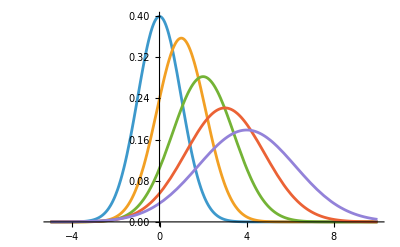

```mathematica
Plot[Evaluate@Table[DensidadProbabilidadSimplificada[xx,tt],{tt,0,4,1}],{xx,-5,10},PlotRange->All]
```

```mathematica
g[t_]:=ParametricPlot3D[{x,t,DensidadProbabilidadSimplificada[x,t]},{x,-5,10},PlotPoints->10]
```

```mathematica
Monitor[Show[Table[{g[i],Graphics3D[Dashing[{0.01,0.01}],Line[{{-5,i,0},{10,i,0}}]]},{i,0,7}],PlotRange->{{-5,10},{0,7},{0,1}},ViewPoint->{0.1,-1.8,0},BoxRatios->{1,2,0.5},Boxed->False],ProgressIndicator[i,{0,7}]]
```

$Aborted

```mathematica
Show[Table[Echo[i,"Procesando i = "];{g[i],Graphics3D[Dashing[{0.01,0.01}],Line[{{-5,i,0},{10,i,0}}]]},{i,0,7}],PlotRange->{{-5,10},{0,7},{0,1}},ViewPoint->{0.1,-1.8,0},BoxRatios->{1,2,0.5},Boxed->False]
```

Procesando i =   0

$Aborted

```mathematica
Dynamic[Refresh[i,UpdateInterval->0.1]]

Show[Table[{g[i],Graphics3D[Dashing[{0.01,0.01}],Line[{{-5,i,0},{10,i,0}}]]},{i,0,7}],PlotRange->{{-5,10},{0,7},{0,1}},ViewPoint->{0.1,-1.8,0},BoxRatios->{1,2,0.5},Boxed->False]
```

$Aborted